## Section 5.1

### Problem 2:

(a)

```mathematica
R={{y, 9, 8.9, 8.75, 8.5, 8.25, 7.75, 7.25, 6.6, 6, 5, 4, 2.75, 1}, {x, 0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12}}
```

{{y,9,8.9,8.75,8.5,8.25,7.75,7.25,6.6,6,5,4,2.75,1},{x,0,1,2,3,4,5,6,7,8,9,10,11,12}}

```mathematica
L=Sum[2R[[1]][[2*i]],{i,1,6}]
```

86.5

```mathematica
R=Sum[2R[[1]][[2*i]],{i,2,7}]
```

70.5

```mathematica
M=Sum[2R[[1]][[2*i+1]],{i,1,6}]
```

79.

(b) Left estimate is an overestimate. The rectangles are above the graph of the function, since the function is decreasing.

(c) Right estimate is an underestimate. The rectangles are below the graph of the function, since the function is decreasing.

(d) The midpoint estimate is the best estimate, as the region underestimated (areas between the left endpoint and the midpoint) and the region overestimated (areas between the midpoint and right endpoint) are roughly the same.

◀     |     ▶

### Problem 18:

The range of values for x is the interval [4,7]. When subdividing this interval into n subintervals, each of them has length

Δx=3/n.

We will use right-endpoints as our sampling points. They have the following expression

x_i=4+(3i)/n

The Riemann sum with this choice of sampling points is

```mathematica
TraditionalForm[
HoldForm[
Limit[
Sum[
(3/n)*((4+(3i)/n)^2+Sqrt[1+2(4+(3i)/n)]),
{i,1,n}],
n-> ∞] ]]
```

(∑_(i=1)^n (3 ((4+(3 i)/n)^2+√(1+2 (4+(3 i)/n))))/n)n∞

◀     |     ▶

### Problem 20:

There are various ways of displaying this region (depending on the choice of function, the position of the sampling points, etc...).  My choice is the function f(x)=x^10. The factor of 2/n leads to an interval of length 2. When interpreting the sampling points as right-endpoints, we are lead to the interval [5,7]. Below is a plot of the region (note: due to the large values of the function, some of the graph was clipped at the top).

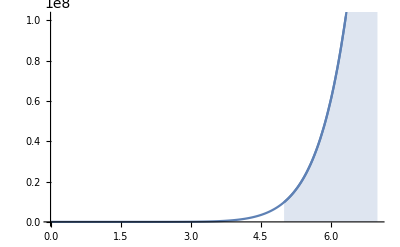

```mathematica
Show[
Plot[x^10,{x,0,7}],
Plot[x^10, {x,5,7}, Filling->Bottom]
]
```

◀     |     ▶

### Problem 22:

(a)

```mathematica
TraditionalForm[
HoldForm[
Limit[
Sum[i^3/n^4,
{i,1,n}],
n-> ∞]
]
]
```

(∑_(i=1)^n i^3/n^4)n∞

(b) We make use of the formula for the sum of cubes given in the textbook,

```mathematica
TraditionalForm[HoldForm[Limit[Sum[i^3/n^4,{i,1,n}],n-> ∞]== Limit[Sum[(n*(n+1))^2/(4n^4),{i,1,n}],n-> ∞]==1/4 ]]
```

(∑_(i=1)^n i^3/n^4)n∞==(∑_(i=1)^n (n (n+1))^2/(4 n^4))n∞==1/4

◀     |     ▶

## Section 5.2

### Problem 18:

The format of the limit,

```mathematica
TraditionalForm[
HoldForm[
Limit[
Sum[Cos[Subscript[x, i]]/Subscript[x, i] Δx,
{i,1,n}],
n-> ∞]
]
]
```

(∑_(i=1)^n (cos(x_i) Δx)/x_i)n∞

suggests that the integrand is the function

```mathematica
TraditionalForm[Cos[x]/x]
```

(cos(x))/x

The region of integration was given, [ℼ,2ℼ], so we infer that this limit is the Riemann sum corresponding to the integral

```mathematica
TraditionalForm[
HoldForm[
Integrate[
Cos[x]/x,
{x,Pi,2*Pi}]
]
]
```

∫_π^(2 π) (cos(x))/x ⅆx

◀     |     ▶

### Problem 28:

We will choose to represent this integral as a limit of right-endpoint sums. The interval fo integration has length 9, so the width of each rectangle is

Δx=9/n

The right-endpoints take the form

x_i=1+(9i)/n

Thus the integral can be written as the following limit:

```mathematica
TraditionalForm[HoldForm[Integrate[(x-4 Log[x]),{x,1,10}]==Limit[Sum[9/n(1+(9i)/n-4Log[1+(9i)/n]),{i,1,n}],n-> ∞]]]
```

∫_1^10 (x-4 log(x))ⅆx==(∑_(i=1)^n (9 (1+(9 i)/n-4 log(1+(9 i)/n)))/n)n∞

◀     |     ▶

### Problem 35:

The region whose area we are interested in is bounded by a semicircle, with center at the origin, and radius 2.

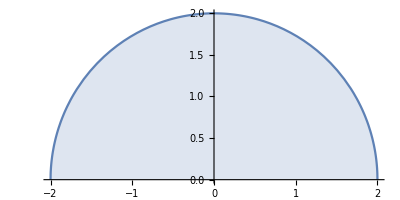

```mathematica
Plot[Sqrt[4-x^2], {x,-2,2}, AspectRatio->Automatic,Filling->Axis, PlotLegends->"y=√(4 - SuperscriptBox[x, 2])"]
```

The area of this region is 2ℼ.

◀     |     ▶

### Problem 42:

We use the Domain Additivity property:

```mathematica
TraditionalForm[Integrate[f[x],{x,1,5}]== (Integrate[f[x],{x,1,4}]) +(Integrate[f[x],{x,4,5}])]
```

∫_1^5 f(x)ⅆx==∫_1^4 f(x)ⅆx+∫_4^5 f(x)ⅆx

Solving for the desired integral, we get

```mathematica
TraditionalForm[12== (Integrate[f[x],{x,1,4}]) +3.6]
```

12==∫_1^4 f(x)ⅆx+3.6

Hence

```mathematica
TraditionalForm[(Integrate[f[x],{x,1,4}]) == 8.4]
```

∫_1^4 f(x)ⅆx==8.4

◀     |     ▶

### Problem 54:

In view of the factor of 1/n in the expression, we will choose an interval of length 1, the interval [0,1], with right-endpoint sampling points given by x_i=i/n. Thus, the integrand is

f(x)=1/(1+x^2)

And the limit can be written as an integral as follows:

```mathematica
TraditionalForm[
HoldForm[
Integrate[
1/(1+x^2),
{x,0,1}]
]
]
```

∫_0^1 1/(1+x^2)ⅆx

◀     |     ▶

## Section 5.3

### Problem 4:

We apply the power rule to find the antiderivatives,

```mathematica
TraditionalForm[HoldForm[Integrate[
1+u^4/2-(2u^9)/5,
u]]== 
Integrate[
1+u^4/2-(2u^9)/5,
u]
]
```

∫(1+u^4/2-(2 u^9)/5)ⅆu==-u^10/25+u^5/10+u

and apply the Net Change Theorem to find the value of the Definite Integral

```mathematica
TraditionalForm[HoldForm[Integrate[
1+u^4/2-(2u^9)/5,
{u,0,1}]]== 
Integrate[
1+u^4/2-(2u^9)/5,
{u,0,1}]
]
```

∫_0^1 (1+u^4/2-(2 u^9)/5)ⅆu==53/50

◀     |     ▶

### Problem 14:

We recognize the antiderivative of

```mathematica
TraditionalForm[Sec[θ]Tan[θ] ]
```

tan(θ) sec(θ)

as the function

```mathematica
TraditionalForm[Sec[θ]]
```

sec(θ)

Applying the Net Change Theorem, we get

```mathematica
TraditionalForm[
HoldForm[
Integrate[Sec[θ]Tan[θ], {θ,0,Pi/4}
]]
== Integrate[Sec[θ]Tan[θ], {θ,0,Pi/4}]]
```

∫_0^(π/4) sec(θ) tan(θ)ⅆθ==√2-1

◀     |     ▶

### Problem 20:

We recognize the antiderivative as

```mathematica
TraditionalForm[HoldForm[Integrate[10^x, x]]== Integrate[10^x,x]]
```

∫10^x ⅆx==10^x/(log(10))

Applying the Net Change Theorem, we get

```mathematica
TraditionalForm[HoldForm[Integrate[10^x, {x,0,1}]]== Integrate[10^x,{x,0,1}]]
```

∫_0^1 10^x ⅆx==9/(log(10))

◀     |     ▶

### Problem 22:

We recognize the antiderivative as

```mathematica
TraditionalForm[HoldForm[Integrate[4/(t^2+1), t]]== Integrate[4/(t^2+1), t]]
```

∫4/(t^2+1)ⅆt==4 tan^-1(t)

Applying the Net Change Theorem, we obtain

```mathematica
TraditionalForm[HoldForm[Integrate[4/(t^2+1),{t,0,1}]]== Integrate[4/(t^2+1), {t,0,1}]]
```

∫_0^1 4/(t^2+1)ⅆt==π

◀     |     ▶

### Problem 24:

We begin by simplifying the integrand

```mathematica
TraditionalForm[HoldForm[(Sin[θ]+Sin[θ]Tan[θ]^2)/(Sec[θ]^2)]== Simplify[(Sin[θ]+Sin[θ]Tan[θ]^2)/(Sec[θ]^2)]]
```

(sin(θ)+sin(θ) tan^2(θ))/(sec^2(θ))==sin(θ)

Now we easily recognize the antiderivative

```mathematica
TraditionalForm[-Cos[θ]]
```

-cos(θ)

and apply the Net Change Theorem to compute the definite integral

```mathematica
TraditionalForm[HoldForm[Integrate[(Sin[θ]+Sin[θ]Tan[θ]^2)/(Sec[θ]^2),{θ,0,Pi/3}] ]== Integrate[(Sin[θ]+Sin[θ]Tan[θ]^2)/(Sec[θ]^2),{θ,0,Pi/3}]]
```

∫_0^(π/3) (sin(θ)+sin(θ) tan^2(θ))/(sec^2(θ))ⅆθ==1/2

◀     |     ▶

### Problem 40:

The derivative of the expression on the right-hand side is

```mathematica
TraditionalForm[(ⅆ(x*Sin[x]+Cos[x]+C))/ⅆx== HoldForm[Sin[x]+x*Cos[x]-Sin[x]]== x*Cos[x]]
```

(ⅆ(C+x sin(x)+cos(x)))/ⅆx==sin(x)+x cos(x)-sin(x)==x cos(x)

This coincides with the integrand on the left, so the formula is correct, according to the Fundamental Theorem of Calculus.

◀     |     ▶

### Problem 48:

First we simplify the integrand

```mathematica
TraditionalForm[HoldForm[Sin[2*x]/Sin[x]]== Simplify[Sin[2*x]/Sin[x]]]
```

(sin(2 x))/(sin(x))==2 cos(x)

Now we recognize the antiderivatives

```mathematica
TraditionalForm[HoldForm[Integrate[Sin[2*x]/Sin[x], x]]== Integrate[Sin[2*x]/Sin[x], x] + C]
```

∫(sin(2 x))/(sin(x))ⅆx==C+2 sin(x)

◀     |     ▶

### Problem 76:

We start by rewriting the sum in compact form:

```mathematica
TraditionalForm[HoldForm[Limit[(Sum[(1/n)Sqrt[i/n], {i,1,n}]),n-> ∞]]]
```

(∑_(i=1)^n (√(i/n))/n)n∞

Thinking of this sum as a right-endpoint sum, the endpoints are

x_i=i/n

We now recognize the function being integrated as

f(x)=√x

The integral is thus

```mathematica
TraditionalForm[HoldForm[Integrate[Sqrt[x],{x,0,1}]]]
```

∫_0^1 √x ⅆx

◀     |     ▶

## Section 5.4

### Problem 6:

The region whose area is represented by the integral, within the range x ∈[0,10], is

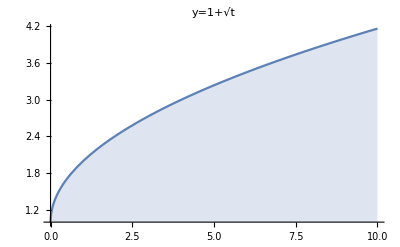

```mathematica
Plot[1+Sqrt[t],{t,0,10}, PlotRange->Full, Filling->Axis, PlotLabel->"y=1+√t"]
```

(a) Using the fundamental theorem of Calculus, we see that

```mathematica
TraditionalForm[
HoldForm[
(ⅆ(Integrate[1+Sqrt[t], {t,0,x}]))/ⅆx]== 1+Sqrt[x]]
```

ⅆ/ⅆx∫_0^x (1+√t)ⅆt==√x+1

(b) An antiderivative of f(t)=1+√t is given by

```mathematica
TraditionalForm[HoldForm[Integrate[1+Sqrt[t], t]]== Integrate[1+Sqrt[t], t]]
```

∫(1+√t)ⅆt==(2 t^(3/2))/3+t

Thus, by the Net Change Theorem,

```mathematica
TraditionalForm[g[x]== 
HoldForm[
Integrate[1+Sqrt[t], {t,0,x}]]== Integrate[1+Sqrt[t], {t,0,x}]]
```

g(x)==∫_0^x (1+√t)ⅆt==(2 x^(3/2))/3+x

Direct differentiation now gives

```mathematica
TraditionalForm[HoldForm[(ⅆ(2x^(3/2)/3+x))/ⅆx]== D[2x^(3/2)/3+x,x]]
```

ⅆ/ⅆx((2 x^(3/2))/3+x)==√x+1

◀     |     ▶

### Problem 14:

In this problem, we cannot use the Fundamental Theorem of Calculus directly, as the top limit of integration is not the same as the variable o Differentiation, but rather a function of it. We appeal to the chain rule. Let

y=x^2

Then

ⅆh/ⅆx=ⅆh/ⅆy ⅆy/ⅆx

So we get

```mathematica
TraditionalForm[ⅆh/ⅆx== (2*x) (HoldForm[((ⅆ(Integrate[Sqrt[1+r^3], {r,0,y}]))/ⅆy)])
== 2*x*Sqrt[1+y^3]== 2*x*Sqrt[1+x^6]]
```

ⅆh/ⅆx==2 x ⅆ/ⅆy∫_0^y √(1+r^3)ⅆr==2 x √(y^3+1)==2 x √(x^6+1)

◀     |     ▶

### Problem 16:

We shall once more employ the chain rule. Before doing so, we rewrite the integral in the usual convention

```mathematica
TraditionalForm[ HoldForm[Integrate[Sin[t]^3,{t,e^x,0}]== -Integrate[Sin[t]^3, {t,0,e^x}]]]
```

∫_(e^x)^0 sin^3(t)ⅆt==-∫_0^(e^x) sin^3(t)ⅆt

Now we use the substitution

z=e^x

Then

```mathematica
TraditionalForm[ⅆy/ⅆx==Exp[x]* (HoldForm[((ⅆ(-Integrate[Sin[t]^3, {t,0,z}]))/ⅆz)])
==-Exp[x]*(Sin[z]^3)==- Exp[x]*(Sin[Exp[x]]^3)]
```

ⅆy/ⅆx==ⅇ^x ⅆ/ⅆz(-∫_0^z sin^3(t)ⅆt)==-ⅇ^x sin^3(z)==-ⅇ^x sin^3(ⅇ^x)

◀     |     ▶

### Problem 22:

We will find the derivative symbolically first

ⅆg/ⅆy(y)= f(y),

(ⅆ^2 g)/(ⅆ y^2)(y)=ⅆf/ⅆy(y)=(ⅆsin(y))/ⅆy (ⅆ(∫_0^z √(1+t^2)ⅆt))/ⅆz= cos(y)√(1+z^2)=cos(y)√(1+sin^2(y))

Hence, for y=ℼ/6, we get

(ⅆ^2 g)/(ⅆ y^2)(ℼ/6)=(√3)/2 √(1+1/4)=(√15)/4

◀     |     ▶

### Problem 32:

(a) The critical numbers of C occur when its derivative, relative to t, is equal to 0. A direct computation, using the product rule and the Fundamental Theorem of Calculus yields

```mathematica
TraditionalForm[(ⅆC/ⅆt)[t]== HoldForm[(ⅆ((1/t)*Integrate[f[s]+g[s],{s,0,t}]))/ⅆt]== ((f[t]+g[t])-"C(t)")/t^2]
```

ⅆC/ⅆt(t)==ⅆ/ⅆt(∫_0^t (f(s)+g(s))ⅆs)/t==(-C(t)+f(t)+g(t))/t^2

This fraction is zero if and only if its numerator vanishes, i.e.,

C(t)=f(t)+g(t),

as we wanted to show.

(b) With the given data, we compute the Total Depreciation function, for values of t between 0 and 30:

```mathematica
TraditionalForm["D"[t]== HoldForm[Integrate[V/15-(Vs)/450, {s,0,t}]]== Integrate[V/15-(V*s)/450, {s,0,t}]]
```

D(t)==∫_0^t (V/15-Vs/450)ⅆs==(t V)/15-(t^2 V)/900

Setting this equal to V yields t=30.

(c)

```mathematica
fn[t_]:=Piecewise[{{1/15-t/450+t^2/12900,t<30},{t^2/12900, t>30}}]
```

```mathematica
int=(Integrate[fn[t],t])
```

Piecewise[{{(2580 t-43 t^2+t^3)/38700, t≤30}, {1+t^3/38700, True}}]

```mathematica
A[t_]:=(1/t)*int
```

```mathematica
Solve[A[t]== fn[t],t]
```

{{t→0},{t→43/2}}

(d) The functions are graphed below.

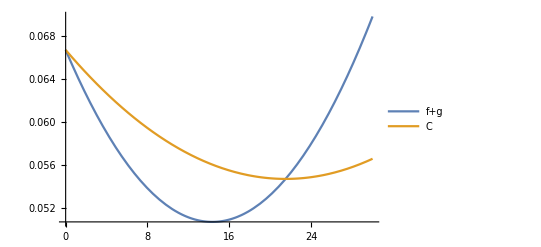

```mathematica
Plot[{fn[t],A[t]}, {t,0,30}, PlotLegends->{"f+g","C"}]
```

◀     |     ▶

## Integration

### The substitution rule

We have seen before that the integral of a product of functions is not equal to the product of the corresponding integrals. The substitution rule is one of the methods to deal with such integrals.

It is based on the chain rule:

(f(g(x)))'=f'(g(x))g'(x)

Integration on both sides followed by an application of the Fundamental Theorem of Calculus yields the substitution formula

```mathematica
TraditionalForm[HoldForm[f[g[x]]]== HoldForm[Integrate[f'[g[x]]*g'[x],x]]]
```

f(g(x))==∫f'(g(x)) g'(x)ⅆx

◀     |     ▶

## Integration

### Integration by parts

This is another technique aimed at solving integrals of products. It is based on the product rule,

```mathematica
TraditionalForm[HoldForm[(f[x]*g[x])']== HoldForm[f'[x]*g[x]+f[x]*g'[x]]]
```

(f(x) g(x))'==f'(x) g(x)+f(x) g'(x)

Integration on both sides, followed by an application of the Fundamental Theorem of Calculus,  yields the integration by parts formula,

```mathematica
TraditionalForm[HoldForm[(f[x]*g[x])]== HoldForm[Integrate[f'[x]*g[x],x]]+HoldForm[Integrate[f[x]*g'[x],x]]]
```

f(x) g(x)==∫f'(x) g(x)ⅆx+∫f(x) g'(x)ⅆx

◀     |     ▶